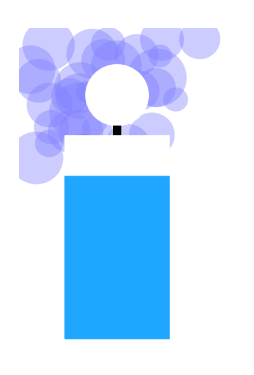

```mathematica
Graphics[{
Table[{Opacity[(*RandomReal[{0.1,0.45}]*)0.4,Lighter[Blue,0.5]],Disk[{RandomReal[{-0.2,0.7}],RandomReal[{0.8,1.5}]},RandomReal[{0.05,0.15}]]
},{30}],
(*container*){EdgeForm[Thick],White,Rectangle[{0,0},{0.5,1}]},
{EdgeForm[Thick],RGBColor[0.12,0.65,1.],Rectangle[{0,0},{0.5,0.8}]},
(*display*)Rectangle[{0.23,1},{0.27,1.05}],{EdgeForm[Thick],White,Disk[{0.25,1.2},0.15]},

},ImageSize->{255,375},PlotRange->{{-0.2,0.8},{-0.01,1.5}}]
```